```mathematica
testFileName = "/Users/dmsussma/repos/useCellGPU/imageTest/data/vertexTest.nc";
```

```mathematica
Import[testFileName,"Datasets"]
```

{pos,force,VertexCellNeighbors,Vneighs,cellType,director,cellPositions,BoxMatrix,meanQ,time}

```mathematica
f=Import[testFileName,"Data"];
nCells=Length[f[[1,1]]]/4
nVertices=nCells*2
boxSideLength=f[[8,1,1]]
frames=Length[f[[1]]]
```

200

400

14.1421

1002

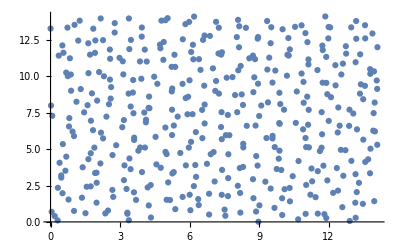

```mathematica
frame=701;
(* grab the positions of vertices in one of the frames*)
pos=Table[{f[[1,frame,2*i+1]],f[[1,frame,2*i+2]]},{i,0,nVertices-1}];
ListPlot[pos]
cellPos=Table[{f[[7,frame,2*i+1]],f[[7,frame,2*i+2]]},{i,0,nCells-1}];
```

```mathematica
(* what are the neighbors of each of the vertices (using the Vneighs data structure) -- note that the "+{1,1,1}" thing is due to the fact that cpp vectors are zero-indexed and mathematica vectors are one-indexed*)
neighs=Table[{1,1,1}+{f[[4,frame,3*i+1]],f[[4,frame,3*i+2]],f[[4,frame,3*i+3]]},{i,0,nVertices-1}];

(* Use this data to just draw lines between the positions of the vertices *)
lines={};
Do[
Do[
bond = {i,neighs[[i,j]]};
If[bond[[1]]<bond[[2]],
p1=pos[[bond[[1]]]];
p2=pos[[bond[[2]]]];
(* If the bond doesn't cross the PBC, keep track of the line.... *)
If[Norm[p1-p2]<boxSideLength/2,
AppendTo[lines,
Graphics[Line[{p1,p2}]]
],
(*else put a poly on the edge*)
pdist=p1-p2;
If[pdist[[1]]>boxSideLength/2,pdist[[1]]-=boxSideLength];
If[pdist[[1]]<-boxSideLength/2,pdist[[1]]+=boxSideLength];
If[pdist[[2]]>boxSideLength/2,pdist[[2]]-=boxSideLength];
If[pdist[[2]]<-boxSideLength/2,pdist[[2]]+=boxSideLength];
AppendTo[lines,Graphics[Line[{p1,p1-pdist}]]];
AppendTo[lines,Graphics[Line[{p2,p2+pdist}]]]
];
];
,{j,1,3}];
,{i,1,nVertices}];
```

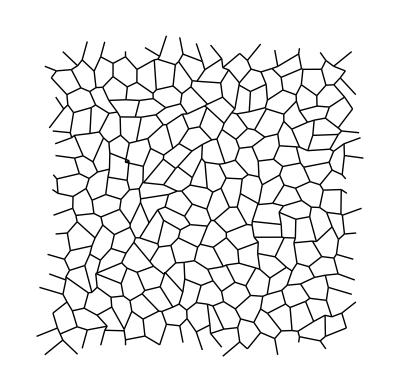

```mathematica
Show[lines]
```

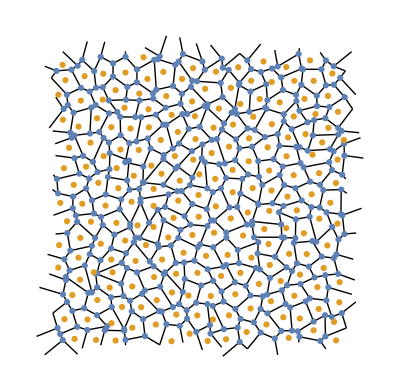

```mathematica
Show[lines,ListPlot[{pos,cellPos}]]
```